```mathematica
(* from RandomAnalyticSignal_Research.nb *)
(* created at 2015/06/14 *)
```

```mathematica
SeedRandom[0]
```

```mathematica
argList[f_,dt_]:=Table[Arg[f[t]],{t,0,2π,dt}];
correct[li_List]:=Rest[li]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[li]];
numberOfExtremum[li_List]:=Length[Select[Differences[li]*RotateRight[Differences[li]],#≤0&]];
inclinationList[f_,dt_]:=Table[Arg[f[t+dt]-c[t]],{t,0,2π,dt}];
breakNumber[li_List]:=Length[Select[Differences[li],#≤-π&]]-Length[Select[Differences[li],#≥π&]] ;
```

```mathematica
lowAmpLi={1,1,1,1,1,0,0,0,0,0};
highAmpLi={0,0,0,0,0,1,1,1,1,1};
```

```mathematica
f[ampLi_List]:=Module[{rotLi=RandomReal[{0,2π},{Length[ampLi]}]},∑_(k=1)^Length[ampLi] ampLi⟦k⟧ Exp[ⅈ k (#-rotLi⟦k⟧)] &];
```

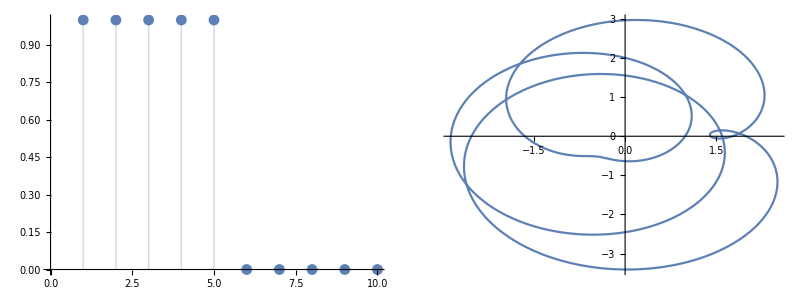

```mathematica
c=f[lowAmpLi];
Grid[{{
ListPlot[lowAmpLi,Filling->Bottom,PlotRange->{0,All}],
ParametricPlot[{Re[#],Im[#]}&[c[t]],{t,0,2π},PlotRange->All]
}}]
```

Rotation:

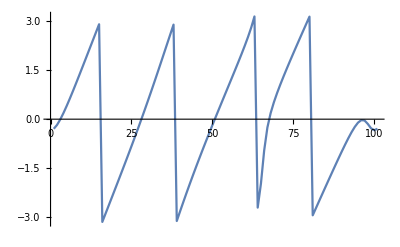

4

```mathematica
(* NumberOfRotation *)
numberOfRotation[f_, dt_]:=breakNumber[inclinationList[f,dt]]
Print["Rotation:"]
ListLinePlot[inclinationList[c,(2π)/100]]
numberOfRotation[c,(2π)/100]
```

ArgExtremum:

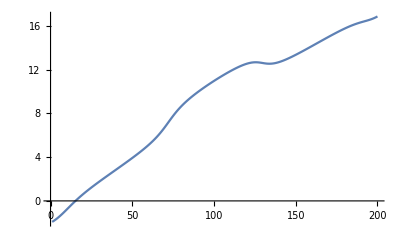

1

```mathematica
(* NumberOfArgExtremum *)
numberOfArgExtremum[f_,dt_]:=numberOfExtremum[correct[argList[f,dt]]]/2;
Print["ArgExtremum:"]
ListLinePlot[correct[argList[c,(2π)/200]]]
numberOfArgExtremum[c,(2π)/200]
```

AbsExtremum:

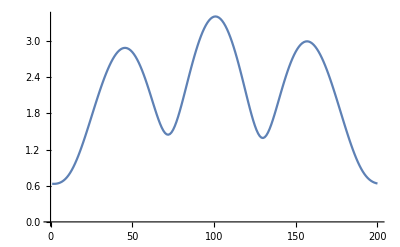

3

```mathematica
(* NumberOfAbsExtremum *)
dt=(2π)/200;
absList=Table[Abs[c[t]],{t,0,2π,dt}];
Print["AbsExtremum:"]
ListLinePlot[correct[absList]]
numberOfExtremum[correct[absList]]/2
```

ReExtremum:

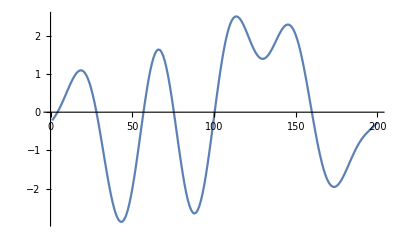

4

```mathematica
(* NumberOfReExtremum *)
dt=(2π)/200;
reList=Table[Re[c[t]],{t,0,2π,dt}];
Print["ReExtremum:"]
ListLinePlot[correct[reList]]
numberOfExtremum[correct[reList]]/2
```

```mathematica
(* Sound *)
Play[Re[c[440*2π*t]],{t,0,1}]
```

-Graphics-